# 0) Preliminaries

```mathematica
plotFun[fun_,lims_,epilog_,label_,legs_:None]:=Framed@Plot[fun,{x,lims[[1,1]],lims[[1,2]]},PlotRange->{Full,{lims[[2,1]],lims[[2,2]]}},Epilog->epilog,PlotLegends->legs,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"x","y"},BaseStyle->{FontSize->20}]
```

```mathematica
discPlotFun[fun_,range_,lims_,epilog_,label_]:=Framed@DiscretePlot[fun,{n,range[[1]],range[[2]]},PlotRange->lims,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}]
```

```mathematica
(*ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,maxran_,limit_,label_,epilog_:{}]:=Module[{funplot,epsplot},
funplot=DiscretePlot[fun[n],{n,0,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}];
epsplot[ϵ_]:=Graphics[{{Line[{{0,limit},{maxran,limit}}],Arrow[{{(*maxran-20*)20,limit+.05},{(*maxran-25*)15,limit}}],Text["lim_(n → ∞) a_n="<>ToString[limit],{(*maxran-20*)22,limit+.05},Left]},{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]},Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]}];
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,.2},0.0001,.2,Appearance->"Open" }
]
]*)
```

# 1) Orthonormalisierung

a)
v_1=(1
-1
1
0
1), v_2=(-1
3
-2
1
-2), v_3=(2
1
1
0
2)
Gram-Schmidtsches Orthogonalisierungsverfahren
u_1, u_2, u_3=?

b)
v_1=(1
ⅈ
0
1), v_2=(3
2ⅈ
ⅈ
1), v_3=(-ⅈ
2
2
0)
Gram-Schmidtsches Orthogonalisierungsverfahren
u_1, u_2, u_3=?

## Gram-Schmidtsches Orthogonalisierungsverfahren geometrically

The vectors in the task are four-dimensional, so let us illustrate the Gram-Schmidtsches Orthogonalisierungsverfahren in two and three dimensions only to be able to see it graphically.

## 2D

Below one can see two vectors that together span a two-dimensional plane:

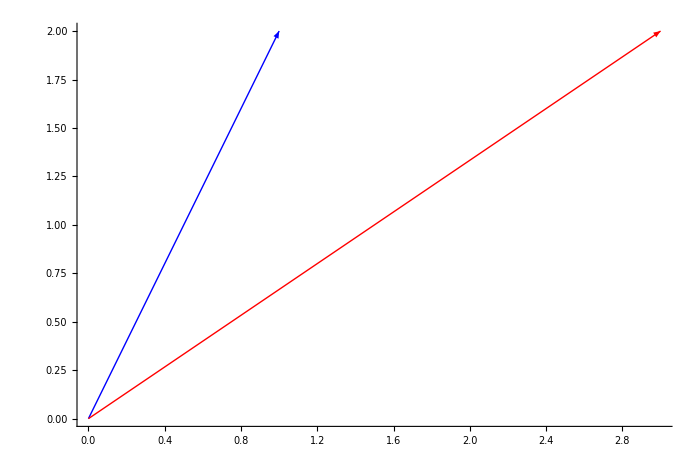

```mathematica
v1={1,2};
v2={3,2};
u1=v1/Norm[v1];
v2par=Projection[v2,u1];
v2ort=v2-v2par;
Graphics[{{Blue, Thick,Arrow[{{0,0},{1,2}}]},{Red, Thick,Arrow[{{0,0},{3,2}}]}},Axes->True,BaseStyle->Large,ImageSize->700]
```

Obviously, these two vectors are not orthonormal. They are not orthogonal and their lengths are not equal to one. It is much more convenient to work with orthonormal vectors though, because for them many mathematical relations hold. We can replace these two vectors by other two vectors, which are indeed orthonormal.

We can start by taking the blue vector (let’s call it v_1) and normalize it to get vector u_1, like so:

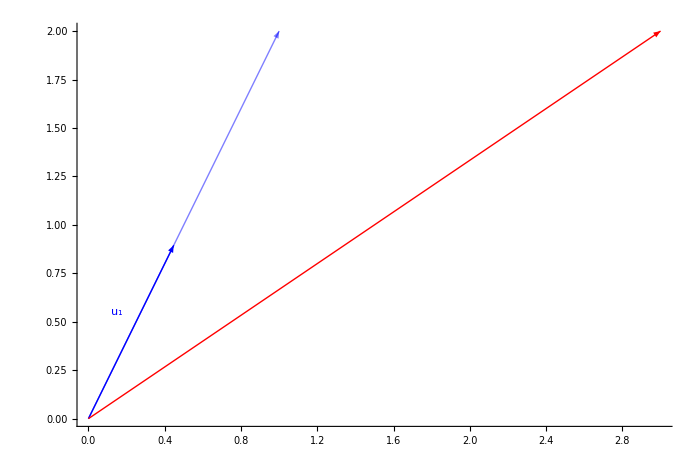

```mathematica
Graphics[{{Blue, Thick,Opacity[.5],Arrow[{{0,0},{1,2}}]},{Blue, Thick,Arrow[{{0,0},1/(√5){1,2}}]},{Style[Text["u_1",{0.15,0.55}],40,Blue]},{Red, Thick,Arrow[{{0,0},{3,2}}]}},Axes->True,BaseStyle->Large,ImageSize->700]
```

At this point we decompose the red vector (let’s call it v_2) into two parts: one part is parallel to the blue vector u_1, the other part is orthogonal to it:

v_2=v_2^par+v_2^ort, where (u_1·v_2^ort)=0. Graphically:

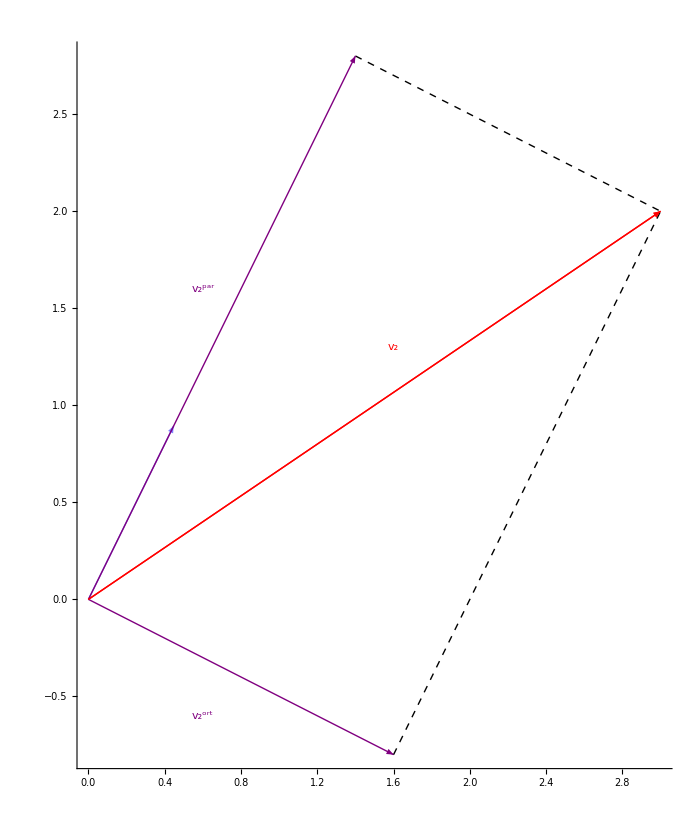

```mathematica
Graphics[{(*{Blue, Thick,Opacity[.5],Arrow[{{0,0},{1,2}}]}*){Blue,Opacity[.5],Thick,Arrow[{{0,0},1/(√5){1,2}}]},(*{Opacity[.5],Style[Text["u_1",{0.15,0.55}],40,Blue]},*){Style[Text["v_2^par",{0.6,1.6}],40,Purple]},{Style[Text["v_2^ort",{0.6,-.6}],40,Purple]},{Style[Text["v_2",{1.6,1.3}],40,Red]},{Purple, Thick,Arrow[{{0,0},v2par}]},{Purple, Thick,Arrow[{{0,0},v2ort}]},{Red, Thick,Arrow[{{0,0},v2}]},{Red, Thick,Arrow[{{0,0},{3,2}}]},
{Black,Dashed,Line[{{v2par,v2},{v2ort,v2}}]}
},Axes->True,BaseStyle->Large,ImageSize->700]
```

To complete the “algorithm” we just take only the part v_2^ort and normalize it to get:

u_1=v_1/(||v_1||)   and   u_2=v_2^ort/(||v_2^ort||)

Vectors u_1 and u_2 are both unit vectors and are also orthogonal to each other, as we wanted. The Gram-Schmidtsches Orthogonalisierungsverfahren is thus finished. Graphically we have now:

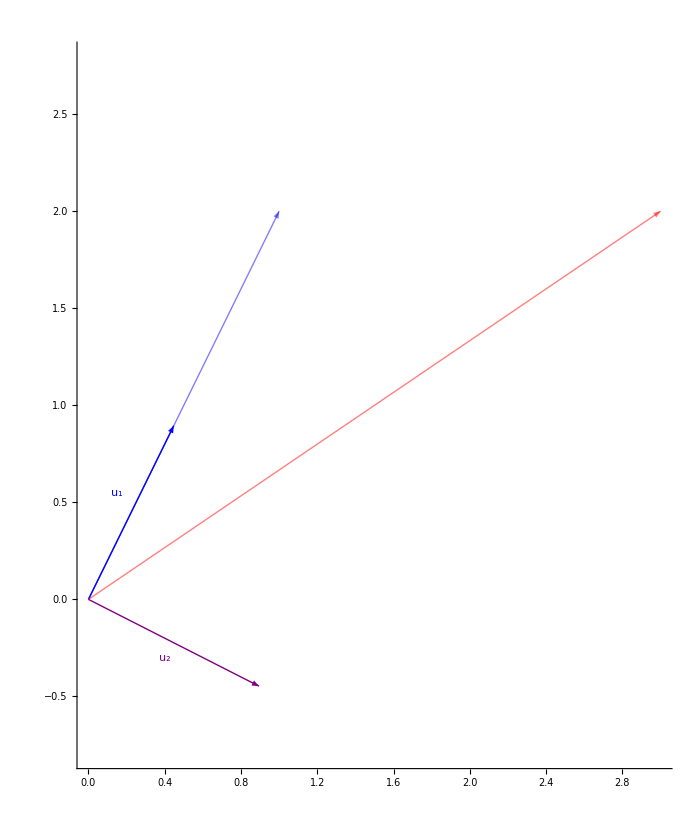

```mathematica
Graphics[{{Blue, Thick,Opacity[.5],Arrow[{{0,0},v1}]},{Blue,Thick,Arrow[{{0,0},1/(√5){1,2}}]},{Style[Text["u_1",{0.15,0.55}],40,Blue]},(*{Style[Text["v_2^par",{0.6,1.6}],40,Purple]},*){Style[Text["u_2",{0.4,-.3}],40,Purple]},(*{Style[Text["v_2",{1.6,1.3}],40,Red]},*)(*{Purple, Thick,Arrow[{{0,0},v2par}]},*){Purple, Thick,Arrow[{{0,0},Normalize@v2ort}]}(*,{Red, Thick,Arrow[{{0,0},v2}]}*),{Red,Opacity[.5],Thick,Arrow[{{0,0},v2}]}(*,
{Black,Dashed,Line[{{v2par,v2},{v2ort,v2}}]}*)
},Axes->True,BaseStyle->Large,ImageSize->700,PlotRange->{{0.,3.},{-0.8,2.8}}]
```

## Mathematics for 2D

We got: v_2=v_2^par+v_2^ort, where (u_1·v_2^ort)=0. Also v_2^par is parallel to u_1 and therefore it is a multiple of u_1 for some coefficient α in the following way: v_2^par=α·u_1.

We can actually calculate the value of α by taking the scalar product of v_2 with u_1 (also remember that u_1 is a unit vector):

(u_1·v_2)=(u_1·(v_2^par+v_2^ort))=(u_1·v_2^par)+(u_1·v_2^ort)=(u_1·(α·u_1))+0=α·||u_1(||)^2=α

Putting all results together we obtain:

v_2=v_2^par+v_2^ort=α·u_1+v_2^ort=(u_1·v_2)·u_1+v_2^ort

From this formula we can calculate v_2^ort as:

v_2^ort=v_2-(u_1·v_2)·u_1

which is exactly the first formula of the Gram-Schmidtsches Orthogonalisierungsverfahren. To get u_2 we just normalize v_2^ort.

## 3D

Similarly to the 2D case, we get the very first vector u_1 by normalizing vector v_1. The second vector v_2 can then be written in the form:

v_2=v_2^par+v_2^ort

We proceed the same way as in the 2D case to get:

v_2^ort=v_2-(u_1·v_2)·u_1   and u_2=v_2^ort/(||v_2^ort||)

The third vector can be decomposed into three parts now: one part is parallel to u_1, one part is parallel to u_2, and the last part is orthogonal to both u_1 and u_2:

v_3=α·u_1+β·u_2+v_3^ort

As in the 2D case, we would calculate that α=(u_1·v_3) and β=(u_2·v_3), so:

v_3=(u_1·v_3)·u_1+(u_2·v_3)·u_2+v_3^ort

The last part v_3^ort is therefore equal to

v_3^ort=v_3-(u_1·v_3)·u_1-(u_2·v_3)·u_2

which is the second formula in the Gram-Schmidtsches Orthogonalisierungsverfahren. We can apply this procedure even for higher dimensions than 3D in an analogous way.

## Solution

## a)

We have freedom to choose the first vector in the new orthonormal basis, so we choose normalized v_1:

u_1:=v_1/(||v_1||)=1/2(1
-1
1
0
1)

The next vector u_2 is a multiple of:

v_2-(u_1·v_2)u_1=(-1
3
-2
1
-2)-(-4)1/2(1
-1
1
0
1)=(-1+2
3-2
-2+2
1+0
-2+2)=(1
1
0
1
0)

where we used result:

(u_1·v_2)=(v_2·u_1)=(-1 | 3 | -2 | 1 | -2)·1/2(1
-1
1
0
1)=1/2(-1-3-2+0-2)=-4

After normalization we get:

u_2:=(v_2-(u_1·v_2)u_1)/(||v_2-(u_1·v_2)u_1||)=1/(√3)(1
1
0
1
0)

The third vector is obtained analogously as a multiple of

v_3-(u_1·v_3)u_1-(u_2·v_3)u_2=(2
1
1
0
2)-(2)1/2(1
-1
1
0
1)-(√3)1/(√3)(1
1
0
1
0)=(2-1-1
1+1-1
1-1+0
0+0-1
2-1+0)=(0
1
0
-1
1)

where we used results:

(u_1·v_3)=(v_3·u_1)=(2 | 1 | 1 | 0 | 2)·1/2(1
-1
1
0
1)=1/2(2-1+1+0+2)=2

(u_2·v_3)=(v_3·u_2)=(2 | 1 | 1 | 0 | 2)·1/(√3)(1
1
0
1
0)=1/(√3)(2+1+0+0+0)=√3

After normalization we get:

u_3:=(v_3-(u_1·v_3)u_1-(u_2·v_3)u_2)/(||v_3-(u_1·v_3)u_1-(u_2·v_3)u_2||)=1/(√3)(0
1
0
-1
1)

## b)

We proceed the exact same way as in a), but here we just have to be careful to complex conjugate the first vector in each scalar product. So

u_1:=v_1/(||v_1||)=1/(√3)(1
ⅈ
0
1)

(u_1·v_2)*=(v_2·u_1)=(3 | -2ⅈ | -ⅈ | 1)·1/(√3)(1
ⅈ
0
1)=1/(√3)(3+2+0+1)=2 √3

v_2-(u_1·v_2)u_1=(3
2ⅈ
ⅈ
1)-2 √3 1/(√3)(1
ⅈ
0
1)=(3-2
2ⅈ-2ⅈ
ⅈ+0
1-2)=(1
0
ⅈ
-1)

u_2:=(v_2-(u_1·v_2)u_1)/(||v_2-(u_1·v_2)u_1||)=1/(√3)(1
0
ⅈ
-1)

(u_1·v_3)*=(v_3·u_1)=(ⅈ | 2 | 2 | 0)·1/(√3)(1
ⅈ
0
1)=1/(√3)(ⅈ+2ⅈ+0+0)=√3 ⅈ

(u_2·v_3)*=(v_3·u_2)=(ⅈ | 2 | 2 | 0)·1/(√3)(1
0
ⅈ
-1)=1/(√3)(ⅈ+0+2ⅈ+0)=√3 ⅈ

v_3-(u_1·v_3)u_1-(u_2·v_3)u_2=(-ⅈ
2
2
0)-(√3 ⅈ)*1/(√3)(1
ⅈ
0
1)-(√3 ⅈ)*1/(√3)(1
0
ⅈ
-1)=(-ⅈ+ⅈ+ⅈ
2-1+0
2+0-1
0+ⅈ-ⅈ)=(ⅈ
1
1
0)

u_3:=(v_3-(u_1·v_3)u_1-(u_2·v_3)u_2)/(||v_3-(u_1·v_3)u_1-(u_2·v_3)u_2||)=1/(√3)(ⅈ
1
1
0)

# 2) Orthogonale Matrix

a) D orthogonale Matrix mit D^2=𝕀𝕕. Ist D symmetrisch?

b) D=(1/2 | (√3)/2
(√3)/2 | -1/2)
Eigenvektoren v_1, v_2?

c) P_1=v_1 v_1^T=?
     P_2=v_2 v_2^T=?
     P_1+P_2=?
     P_1-P_2=?

### Useful formulas

Orthogonale Matrix

Aᵀ·A=𝕀𝕕

Symmetrische Matrix

Aᵀ=A

Spectral decomposition in 2D

A=λ_1 P_1+λ_2 P_2

λ_1, λ_2 are eigenvalues

P_1 (P_2) is the projector on the eigenspace corresponding to eigenvalue λ_1 (λ_2)

## Solution

## a)

From Dᵀ·D=𝕀𝕕 follows, that D is invertierbar and D^-1=Dᵀ. We multiply by Dᵀ equation D·D=𝕀𝕕 and obtain Dᵀ·D·D=Dᵀ·𝕀𝕕, from where D=Dᵀ

## b)

### Eigenvalues

det(D-λ 𝕀𝕕)=det(1/2-λ | (√3)/2
(√3)/2 | -1/2-λ)=(1/2-λ)(-1/2-λ)-((√3)/2)^2=…=(λ-1)(λ+1)

So λ_1=1 and λ_2=-1.

### Eigenvector for λ_1=1

D-λ_1 𝕀𝕕=(1/2-1 | (√3)/2
(√3)/2 | -1/2-1)∼(-1/2 | (√3)/2
0 | 0)∼(-1 | √3
0 | 0)

And so: v_1∝(√3
1). After normalization: v_1=1/2(√3
1)

### Eigenvector for λ_2=-1

D-λ_2 𝕀𝕕=(1/2+1 | (√3)/2
(√3)/2 | -1/2+1)∼(3/2 | (√3)/2
0 | 0)∼(√3 | 1
0 | 0)

And so: v_2∝(-1
√3). After normalization: v_2=1/2(-1
√3)

## c)

From the eigenvector v_1 corresponding to eigenvalue λ_1 we can create the associated projector like P_1=v_1 v_1^T. We get

P_1=v_1 v_1^T=1/2(√3
1)·1/2(√3 | 1)=1/4(3 | √3
√3 | 1)

This matrix takes arbitrary vector and returns only that part of the vector, which lies in a subspace spanned by eigenvector v_1.

Analogously, for eigenvector v_2 we obtain:

P_2=v_2 v_2^T=1/2(-1
√3)·1/2(-1 | √3)=1/4(1 | -√3
-√3 | 3)

Already at this point, without making further calculations, it should be clear that

P_1+P_2=𝕀𝕕  ...(1)
P_1-P_2=D    ...(2)

The reason for (1) is that P_1 and P_2 are orthogonal projectors for two different eigenvalues in a two-dimensional vector space. So when one takes a random vector w, its part lying in the eigensubspace for eigenvalue λ_1 is equal to w_1=P_1·w. Similarly, its part lying in the eigensubspace for λ_2 is equal to w_2=P_2·w. Since these two parts add up to the original vector, we have:

w=w_1+w_2=P_1·w+P_2·w=(P_1+P_2)·w

As this is true for arbitrary w, we conclude that P_1+P_2=𝕀𝕕.

To see, why (2) holds, we consider a property of symmetric matrices: the spectral decomposition. That is, matrix D can be written as a sum

D=∑_(i=1)^d λ_i P_i

Since in the present case we are dealing with a two-dimensional vector space, we have d=2 and the formula simplifies into

D=λ_1 P_1+λ_2 P_2=P_1-P_2

Anyway, we can get formulas (1) and (2) also by explicit calculation:

P_1+P_2=1/4(3 | √3
√3 | 1)+1/4(1 | -√3
-√3 | 3)=1/4(4 | 0
0 | 4)=(1 | 0
0 | 1)

P_1-P_2=1/4(3 | √3
√3 | 1)-1/4(1 | -√3
-√3 | 3)=1/4(2 | 2 √3
2 √3 | -2)=1/2(1 | √3
√3 | -1)

# 3) Diagonalisierung einer hermiteschen Matrix

A=(2 | -ⅈ | -ⅈ
ⅈ | 2 | -1
ⅈ | -1 | 2)

a) P_A(t)=?, Eigenwerte?

b) Bestimme zu jedem Eigenraum eine Orthonormalbasis.

b)  Bestimme eine unitäre Matrix S, sodass S A S^-1 eine Diagonalmatrix ist.

## Solution

## Eigenvalues

P_A(λ)=det(A-λ 𝕀𝕕)=det(2-λ | -ⅈ | -ⅈ
ⅈ | 2-λ | -1
ⅈ | -1 | 2-λ)=(2-λ)det(2-λ | -1
-1 | 2-λ)-ⅈ det(-ⅈ | -ⅈ
-1 | 2-λ)+ⅈ det(2-λ | -1
-1 | 2-λ)=(2-λ)((2-λ)^2-1)-ⅈ(-ⅈ(2-λ)-ⅈ)+ⅈ ((2-λ)^2-1)=…=-9λ+6 λ^2-λ^3=-λ(λ^2-6λ+9)=-λ(λ-3)(λ-3)

The eigenvalues are thus λ_1=0 and λ_2=3. Let us calculate the eigenvectors.

## Eigenvectors for λ_1=0

A-λ_1 𝕀𝕕=(2 | -ⅈ | -ⅈ
ⅈ | 2 | -1
ⅈ | -1 | 2)~(2ⅈ | 1 | 1
2ⅈ | 4 | -2
2ⅈ | -2 | 4)~(2ⅈ | 1 | 1
0 | 3 | -3
0 | -3 | 3)~(2ⅈ | 1 | 1
0 | 1 | -1
0 | 0 | 0)

From the last matrix we see that the eigenvectors are of the form:

v_1=α·(ⅈ
1
1) for some number α. After normalization we get:

u_1=1/(√3)(ⅈ
1
1)

## Eigenvectors for λ_2=3

A-λ_2 𝕀𝕕=(2-3 | -ⅈ | -ⅈ
ⅈ | 2-3 | -1
ⅈ | -1 | 2-3)=(-1 | -ⅈ | -ⅈ
ⅈ | -1 | -1
ⅈ | -1 | -1)~(1 | ⅈ | ⅈ
0 | 0 | 0
0 | 0 | 0)

From the last matrix we see that the eigenvectors are of the form:

v_2=α·(-ⅈ
0
1)+β·(-ⅈ
1
0) for some numbers α and β.

We define normalized vectors: v_2^(1)=1/(√2)(-ⅈ
0
1)  and v_2^(2)=1/(√2)(-ⅈ
1
0). But these two vectors are not orthogonal to each other. To make it so, we define

u_2:=v_2^(1)=1/(√2)(-ⅈ
0
1)

and find u_3 such that it is orthogonal to u_1 and spans the same eigenspace. To that end we use Gram-Schmidtsches Orthogonalisierungsverfahren like so:

u_3=v_2^(2)-(u_1·v_2^(2))·u_1=1/(√2)(-ⅈ
1
0)-1/2·1/(√2)(-ⅈ
0
1)=1/(√2)(-ⅈ+ⅈ/2
1
-1/2)=1/(√2)(-ⅈ/2
1
-1/2)

where we used result:

(u_1·v_2^(2))†=(v_2^(2)·u_1)=1/(√2)(+ⅈ | 1 | 0)·1/(√2)(-ⅈ
0
1)=1/2(1+0+0)=1/2

We still have to normalize u_3 to obtain:

u_3=1/(√6)(-ⅈ
2
-1)

## Matrices S^-1 and S

We obtained an orthogonal basis of ℂ^3 consisting of vectors (u_1,u_2,u_3). As these vectors are unit vectors and orthogonal to each other, matrix M constructed as

M=(u_1   u_2   u_3)=(ⅈ/(√3) | -ⅈ/(√2) | -ⅈ/(√6)
1/(√3) | 0 | 2/(√6)
1/(√3) | 1/(√2) | -1/(√6))

is unitary. For unitary matrices it holds that M†=M^-1 and so instead of tedious calculation of the inverse matrix we can just transpose it and take its complex conjugate like so:

M^-1=M†=(u_1   u_2   u_3)†=(-ⅈ/(√3) | 1/(√3) | 1/(√3)
ⅈ/(√2) | 0 | 1/(√2)
ⅈ/(√6) | 2/(√6) | -1/(√6))

We can put S:=M† to come to relation:

S·A·S^-1=D, where

D=(λ_1 | 0 | 0
0 | λ_2 | 0
0 | 0 | λ_3)=(0 | 0 | 0
0 | 3 | 0
0 | 0 | 3)